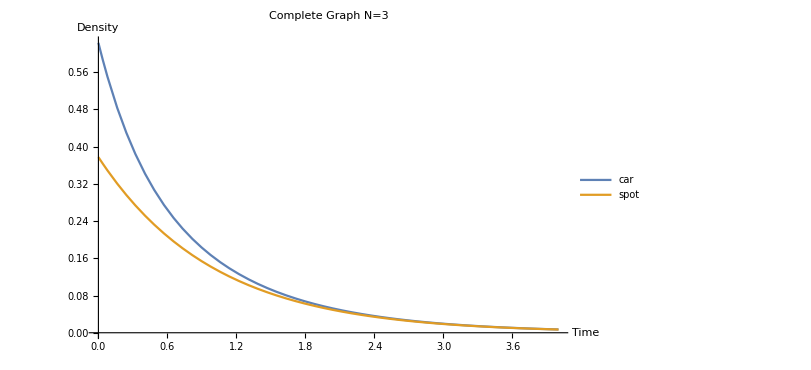

1.65111

```mathematica
Clear[s,x1,x2,x3,c,t]
p=.6228;
sol=NDSolve[{s'[t]==-s[t],
x1'[t]==-(s[t]*x1[t]+x1[t]x2[t]+2*x1[t]^2)/(x1[t]+x2[t]+x3[t]),
x2'[t]==-(s[t]*x2[t]+x1[t]x2[t]-x1[t]^2)/(x1[t]+x2[t]+x3[t]),
x3'[t]==-(s[t]*x3[t]-x1[t]x2[t])/(x1[t]+x2[t]+x3[t]),
c[t]==x1[t]+x2[t]+x3[t],
x1[0]==p,s[0]==1-p,x2[0]==0,x3[0]==0},{s,x1,x2,x3,c},{t,0,20}];
Plot[{(c[t])/.sol,s[t]/.sol},{t,0,4},PlotLegends->{"car","spot"},ImageSize->600,AxesLabel->{HoldForm[Time],HoldForm[Density]},PlotLabel->HoldForm[Complete Graph N=3]]
gamma=p/(1-p)
```

```mathematica
Show[%1228,AxesLabel->{HoldForm[Time],HoldForm[Density]},PlotLabel->HoldForm[Complete Graph N=3],LabelStyle->{GrayLevel[0]}]
```

-Graphics-